# Mathematical modelling and computer simulations in theory and practice

## Project 2 Aleksandra Stachecka

## Title: Falling body

```mathematica
ClearAll["Global`*"]
```

#### Parameters

```mathematica
g=9.81; (* gravitational acceleration, [m/s^2] *)
h=100; (* initial height, [m] *)
v0=0; (* initial speed, [m/s] *)
k=0.9; (* air resistance coefficient, [kg/s] *)
m=1; (* mass of the body, [kg] *)
```

#### First case: Without air resistance and ignoring the mass of the body

```mathematica
(* DSolve does not work properly so we will do all the calculations manually*)
```

```mathematica
(* Integrate y''(t)=g to find y'(t) *)
yPrime[t_]=Integrate[g,t]+v0;
(* Integrate y'(t) to find y(t) *)
y[t_]=Integrate[yPrime[t],t];
(* The result *)
y[t]
```

4.905 t^2

```mathematica
(* Solve for the time T when y(t)=h *)
timeToGroundNoRes=Solve[y[t]==h,t,Reals]
```

{{t→-4.51524},{t→4.51524}}

```mathematica
T=timeToGroundNoRes[[2,1,2]];
```

```mathematica
(* Plot the relation z(t)=h-y(t), distance to the ground over time *)
z[t_]:=h-y[t];
```

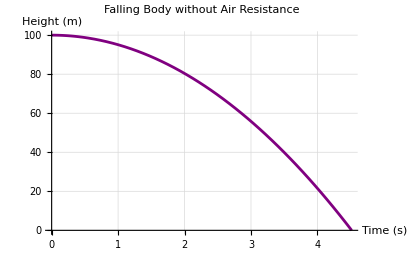

```mathematica
Plot[z[t],{t,0,T},
PlotLabel->"Falling Body without Air Resistance",AxesLabel->{"Time (s)","Height (m)"},
PlotRange->All,
PlotStyle->Purple,
GridLines->Automatic]
```

#### Second case: With air resistance and including the mass of the body

```mathematica
(* again, we will have to solve everything step by step *)
```

```mathematica
(* solve for the velocity v(t):
second order differential equation y''(t)+(k/m)*y'(t)=g 
can be transformed into a first order diff. eq. for velocity *)
```

```mathematica
v[t_]=(v0-(g*m)/k)*Exp[-(k/m)*t]+(g*m)/k;
```

```mathematica
(* integrate the velocity to get the y(t) - we will use f(t) to avoid conflicts with previously defined variables *)
```

```mathematica
f[t_]=Integrate[v[t],t]+c1;
```

```mathematica
(* solve for c1 using the initial condition f(0)=0 *)
```

```mathematica
c1=Solve[f[0]==0,c1][[1,1,2]];
```

```mathematica
(*replace c1 in f(t)*)
```

```mathematica
f[t_]=f[t]/.c1->c1;
```

```mathematica
(* the result *)
```

```mathematica
f[t]
```

-12.1111+12.1111 ⅇ^(-0.9 t)+10.9 t

```mathematica
(* solve for the time T when f(t)=h *)
```

```mathematica
T=Quiet[Solve[f[t]==h,t]][[2,1,2]]
```

10.2853

```mathematica
(* plot the relation z(t)=h-f(t) *)
```

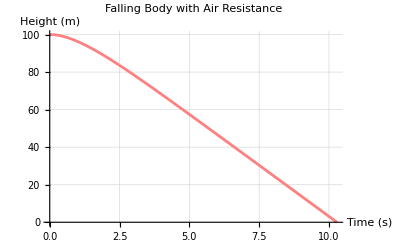

```mathematica
Plot[h-f[t],{t,0,T},
PlotLabel->"Falling Body with Air Resistance",
AxesLabel->{"Time (s)","Height (m)"},
PlotRange->All,
PlotStyle->Pink,
GridLines->Automatic]
```